# Vaje 4

13. 3. 2025

## 1. kolokvij iz Matematike 1

1. Dokaži, da je za vsako naravno število  izraz  deljiv s .

2.  Določi vsa realna števila , ki zadoščajo neenačbi .

```mathematica
Reduce[Abs[x^2+3x+2]+Abs[x+2]>2x^2 + x]
```

-1<x<4

3. V kompleksnih številih reši enačbo . Rešitve nariši v kompleksni ravnini.

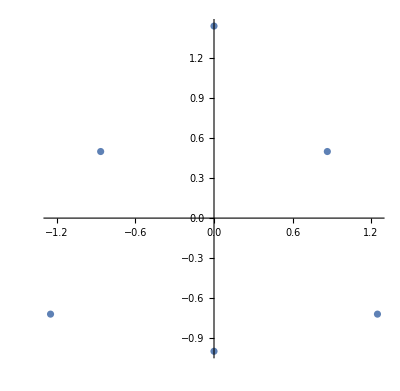

```mathematica
Solve[z^6 + 2I z^3 + 3 == 0, {z}] // Values // Flatten // ComplexListPlot
```

4. Dana je množica . Ugotovi, katere od količin min A, inf A, max A in sup A obstajajo ter jih določi. Vse odgovore natančno utemelji.

```mathematica
A[n_] := (8n + 2)/(4n - 1)
Limit[A[n], n-> Infinity] (* inf*)
Solve[A[n] == 2, n] (* ni min*)
Reduce[A[n + 1] - A[n] < 0, Element[n, Integers]] (* A je padajoč*)
A[1] (*max in sup*)
```

2

{}

n∈ℤ&&(n≤-1||n≥1)

## 2. kolokvij iz Matematike 1

1. Funkcija  je podana s predpisom

 

Izračunaj naravno definicijsko območje funkcije  in izračunaj kompozitum , kjer je 

g funkcija, ki je za  enaka , sicer pa je enaka .

```mathematica
f[x_] := Log[ArcSin[(3+x)/(3x - 1)]]
g[x_] := Piecewise[{
		{Power[E, x], x <= Log[Pi/2]},
		{Power[E,-x ], x> Log[Pi/2]}}]
FunctionDomain[f[x], x]
g[f[x]] // FullSimplify
```

x<-3||x≥2

Piecewise[{{1/ArcSin[(3+x)/(-1+3 x)], Log[ArcSin[(3+x)/(-1+3 x)]]>Log[π/2]}, {ArcSin[(3+x)/(-1+3 x)], True}}]

2. Izračunaj naslednjo limito

.

```mathematica
Limit[(n+2)/(Power[Factorial[n+1], 1/n]), n-> Infinity]
```

ⅇ

3. V odvisnosti od  preuči konvergenco zaporednja , ki je podano rekurzivno: , , kjer je  naravno število. V primerih ko zaporedje konvergira, zapiši še njegovo limito.

```mathematica
Clear[x]
h[x_] :=((9 - x)x)/6
```

```mathematica
Solve[h[x] == x]
```

{{x→0},{x→3}}

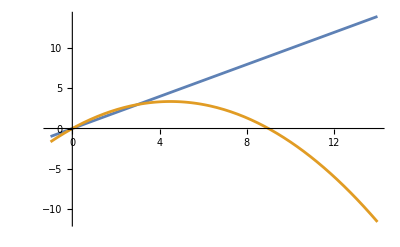

```mathematica
Plot[{x, h[x]}, {x, -1, 14}]
```

4. Poišči vsa realna števila , za katera konvergira vrsta 

.

## 3. kolokvij iz Matematike 1

-Graphics-